## Highly Idealized Models for Host-Pathogen Interactions and Evolution

### Exact-match fitness functions (SW)

https://writings.stephenwolfram.com/2024/12/foundations-of-biological-evolution-more-results-more-surprises/#exact-match-fitness-functions

```mathematica
arast=1-Sign[ImageData[ImageCrop[Binarize@-Graphics-(*Rasterize[Style["A",Bold],RasterSize->{30,30}]*)]]];
```

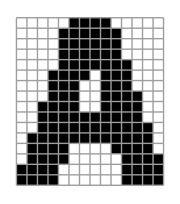

```mathematica
ArrayPlot[arast,Mesh->True, ImageSize->Small]
```

```mathematica
{{"[◼]", "patternevolve"}}[array_,init_,tmax_]:=Module[{ru,mo},NestList[(ru={{"[◼]", "RandomRuleMutation"}}[First[#]];If[(mo={{"[◼]", "MatrixOverlap"}}[CellularAutomaton[ru,CenterArray[{1},Last[Dimensions[array]]],First[Dimensions[array]]-1],array])>=Last[#],{ru,mo},#])&,{init,-Infinity},tmax]]
```

```mathematica
Column[GraphicsRow/@ParallelTable[(SeedRandom[242424+i];First/@Split[With[{array=arast},ArrayPlot[CellularAutomaton[First[#],CenterArray[{1},Last[Dimensions[array]]],First[Dimensions[array]]-1],ImageSize->35]&/@(First/@Split[{{"[◼]", "patternevolve"}}[array,{0,2,2},1000]])]]),{i,{10,15,19,30,44,52,94}}],Spacings->1]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

### Computer security (WN) (also relevant for adapted vs. engineered)

We can frame the fundamental problem of computer security much like the fundamental problem of medicine.

Here we use a special cellular automata discussed in NKS as a model for an idealized software program. What makes this automata unique is that the number of colored cells in the final row are double the number of colored cells in the first row. So we can think of it as doing “useful computation”, which makes it a good minimal model for the computer programs seen in engineering systems:

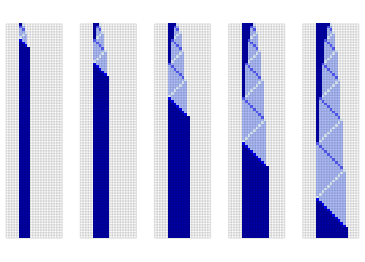

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, ImageSize-> {Automatic, 250}, "InitialIndex"->0]]@@@#]&/@caperts[[{1}]]
]
```

This system, clearly has far more modularity than our adapted systems, and interestingly, we can also observe this in the rules:

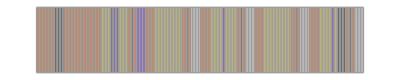

```mathematica
{{"[◼]", "RulesMutationPlot"}}[{{240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}}]
```

But back to computer security, we can then model the attacker as a perturbation to one of the cells in the program.

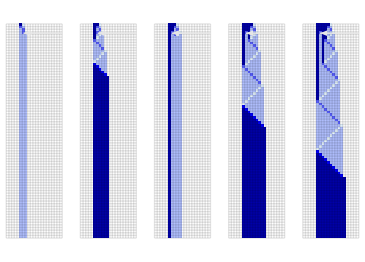

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, ImageSize-> {Automatic, 250}, "InitialIndex"->0]]@@@#]&/@caperts[[{2}]]
]
```

And we can already observe the differing effects of the perturbation, or “classes of attacks”

Similar to the case of medicine, we see “attacks” (second column from the left) that have little effect and some that have an effect on both the ...

One interesting effect I found is it seems that more efficient parallelized programs seem to be more fragile:

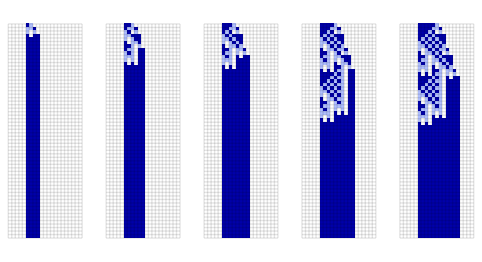
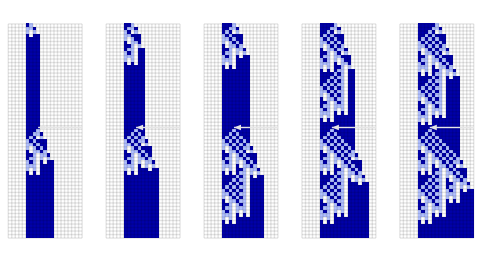

```mathematica
SeedRandom[111000+8];Module[{rule = {837428508144, 3, 1}, ca,capert,  pert = <|{30,9}->2|>, colrules = {0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, caperts},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{60,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, ImageSize-> {Automatic, 250}]]@@@#]&/@caperts
]
```

Curiously, the prime numbers program is remarkably robust:

```mathematica
nonzeroRange[list_]:= SparseArray[list]["ExplicitPositions"] // If[Length[#] == 0, #, {#[[1, 1]], #[[-1, 1]]}]&
```

```mathematica
bodyidxs[ca_List]:= Block[{ranges =DeleteCases[nonzeroRange/@ ca, {}]},
Table[{i, #}&/@ Range@@ranges[[i]], {i, Length[ranges]}]
]
```

```mathematica
Module[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={{10,0,4,8},0},k = 16, r = 1,nperts = 10, ca, bis, vals},
ca = CellularAutomaton[rule,init,{{0,40},{-43,17}}];
bis = RandomChoice[Select[Catenate[bodyidxs[ca]], #[[1]]<20 &&#[[2]] > 45&], nperts]; 
vals = RandomChoice[Delete[Range[0, k - 1], ca[[#1, #2]]+1]]&@@@bis;
Show[{{"[◼]", "PlotCA"}}[{ReplacePart[ca, Thread[bis->vals]], AssociationThread[bis->vals]},ColorRules->Automatic,
 ColorFunction->(If[# == 0, White, Blend[{LightBlue, Blue}, #]]&)], TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameTicks->{Table[{Prime[i] + .5, Prime[i]}, {i, 1,12}], False, False, False}]]
```

-Graphics-

Although if you change the initial conditions its a different story:

```mathematica
With[{rule={{13,3,13}->12,{6,_,4}->15,{10,_,3|11}->15,{13,7,_}->8,{13,8,7}->13,{15,8,_}->1,{8,_,_}->7,{15,1,_}->2,{_,1,_}->1,{1,_,_}->8,{2|4|5,_,_}->13,{15,2,_}->4,{_,4,8}->4,{_,4,_}->5,{_,5,_}->3,{15,3,_}->12,{_,x:2|3|8,_}:>x,{_,x:11|12,_}:>x-1,{11,_,_}->13,{13,_,1|2|3|5|6|10|11}->15,{13,0,8}->15,{14,_,6|10}->15,{10,0|9|13,6|10}->15,{6,_,6}->0,{_,_,10}->9,{6|10,15,9}->14,{_,6|10,9|14|15}->10,{_,6|10,_}->6,{6|10,15,_}->13,{13|14,_,9|15}->14,{13|14,_,_}->13,{_,_,15}->15,{_,_,9|14}->9,{_,_,_}->0},init={MapAt[RandomChoice[Delete[Range[0, 15], # + 1]]&, {10, 0, 4, 8},RandomInteger[{1, 4}]] ,0}},Show[ArrayPlot[CellularAutomaton[rule,init,{{0,40},{-43,40}}],Mesh->None,MeshStyle->GrayLevel[0.3],ImageSize->500], TicksStyle->GrayLevel[.25],FrameTicksStyle->GrayLevel[.25],FrameTicks->{Table[{Prime[i] + 2.5, Prime[i]}, {i, 1,12}], False, False, False}]]
```

-Graphics-

This strikes me as a very interesting study for future work. See https://github.com/willemnielsen/Wolfram/tree/0c039062f89b9bab5e7ca86157794e0e2e5cb0bc/Cryptography for all the notebooks

### Gene transfer

#### SW’s work: https://writings.stephenwolfram.com/2024/05/why-does-biological-evolution-work-a-minimal-model-for-biological-evolution-and-other-adaptive-processes/#an-aside-sexual-reproduction

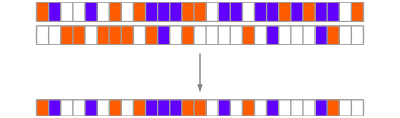

```mathematica
SeedRandom[242442];{{"[◼]", "RandomCrossoverPlot"}}@@Table[
{FromDigits[RandomInteger[2,27],3],3,1},2]
```

#### WN’s Work: https://wolframinstitute.org/output/natures-compass-a-visual-exploration-of-hierarchy-in-biology-and-beyond

```mathematica
SeedRandom[666680 + 11];
hevo = NestList[
Function[evosteps, 
If[!AllSameBy[evosteps,  #fitness&],
Table[First[MaximalBy[evosteps, #fitness&]], Length[evosteps]],
newevosteps = 
With[{nr = {{"[◼]", "RandomRuleMutation"}}[#rule]},
<|"rule"->nr, "fitness"->{{"[◼]", "TestLifetime"}}[nr]|>]&/@ evosteps;
MapThread[If[#2["fitness"] == -Infinity, #1, If[0 <= #2["fitness"] - #fitness<= 1, #2, #]]&, {evosteps, newevosteps}]
]], Table[<|"rule"-> {109636419052937157723438118980837975564,4,1}, "fitness"-> {{"[◼]", "TestLifetime"}}[{109636419052937157723438118980837975564,4,1}]|>, 2], 2000];
```

```mathematica
drf1 = DimensionReduction[IntegerDigits[#rule[[1]],4,64]&/@Catenate[GatherBy[hevo, #[[All, "fitness"]]&][[All, 1]]],Method->"TSNE"];
drs3 = drf1[IntegerDigits[#rule[[1]],4,64]]&/@ GatherBy[hevo, #[[All, "fitness"]]&][[All, 1, 1]];
drs4 = drf1[IntegerDigits[#rule[[1]],4,64]]&/@ GatherBy[hevo, #[[All, "fitness"]]&][[All, 1, 2]];
```

```mathematica
co3 = MapThread[Callout[#1, Pane[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#2["rule"], {{1}, 0},{{"[◼]", "TestLifetime"}}[ #2["rule"]] + 1],ColorRules->{0->GrayLevel[0.15],1->Hue[0.06, 1, 1],2->Hue[0.14, 0.81, 0.99],3->Hue[0.73, 1, 1]} , 
ImageSize->{Automatic, 8Sqrt[1+{{"[◼]", "TestLifetime"}}[#2["rule"]]]}]], Background->None]&, {drs3, GatherBy[hevo, #[[All, "fitness"]]&][[All, 1, 1]]}];
```

```mathematica
co4 = MapThread[Callout[#1, Pane[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#2["rule"], {{1}, 0},{{"[◼]", "TestLifetime"}}[ #2["rule"]] + 1],ColorRules->{0->GrayLevel[0.15],1->Hue[0.06, 1, 1],2->Hue[0.14, 0.81, 0.99],3->Hue[0.73, 1, 1]} , 
ImageSize->{Automatic, 10Sqrt[1+{{"[◼]", "TestLifetime"}}[#2["rule"]]]}]], Background->None]&, {drs4, GatherBy[hevo, #[[All, "fitness"]]&][[All, 1, 2]]}];
```

```mathematica
ListLinePlot[{co3, co4}, Frame->True,Axes->False, PlotHighlighting->None, PlotStyle->{ RGBColor[0.8300000000000001, 0.31, 0.],RGBColor[0.52, 0.65, 0.]}, Mesh->All, FrameTicks->False]
```

-Graphics-

```mathematica
drf1 = DimensionReduction[IntegerDigits[#rule[[1]],4,64]&/@Catenate[GatherBy[evo, #[[All, "fitness"]]&][[All, 1]]],Method->"TSNE"];
drs1 = drf1[IntegerDigits[#rule[[1]],4,64]]&/@ GatherBy[evo, #[[All, "fitness"]]&][[All, 1, 1]];
drs2 = drf1[IntegerDigits[#rule[[1]],4,64]]&/@ GatherBy[evo, #[[All, "fitness"]]&][[All, 1, 2]];
```

```mathematica
co1 = MapThread[Callout[#1, Pane[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#2["rule"], {{1}, 0},{{"[◼]", "TestLifetime"}}[ #2["rule"]] + 1],ColorRules->{0->GrayLevel[0.15],1->Hue[0.06, 1, 1],2->Hue[0.14, 0.81, 0.99],3->Hue[0.73, 1, 1]} , 
ImageSize->{Automatic, 10Sqrt[1+{{"[◼]", "TestLifetime"}}[#2["rule"]]]}]], Background->None]&, {drs1, GatherBy[evo, #[[All, "fitness"]]&][[All, 1, 1]]}];
```

```mathematica
co2 = MapThread[Callout[#1, Pane[ArrayPlot[ArrayPad[#, 1]&/@CellularAutomaton[#2["rule"], {{1}, 0},{{"[◼]", "TestLifetime"}}[ #2["rule"]] + 1],ColorRules->{0->GrayLevel[0.15],1->Hue[0.06, 1, 1],2->Hue[0.14, 0.81, 0.99],3->Hue[0.73, 1, 1]} , 
ImageSize->{Automatic, 10Sqrt[1+{{"[◼]", "TestLifetime"}}[#2["rule"]]]}]], Background->None]&, {drs2, GatherBy[evo, #[[All, "fitness"]]&][[All, 1, 2]]}];
```

```mathematica
ListLinePlot[{co1, co2}, Axes->False, PlotHighlighting->None, Mesh->All, Frame->True, FrameTicks->False]
```

-Graphics-

#### WN’s work on shuffling of initial conditions:

```mathematica
ru = {1246491453600,3,1};
{n, k, r} = ru;
```

```mathematica
SeedRandom[222333];
shuffleevo = NestList[
Function[{init, fitness}, 
newinit = MapAt[RandomChoice[Delete[Range[0, k - 1], #+1]]&, init, RandomInteger[{1, Length@init}]];
inits = Join@@@Permutations[Partition[newinit, UpTo[5]]];
newfitness = Min[{{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru, {#, 0}, {115, All}]]&/@ inits];
If[newfitness>= fitness, {newinit, newfitness}, {init, fitness}]]@@#&,
{CenterArray[{1},20], 1}, 1000];
```

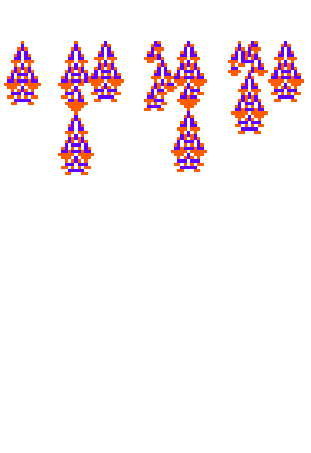

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[ru,{#[[1, 1]], 0},{115, Automatic}], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&/@ GatherBy[shuffleevo, Last]]
```

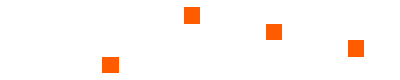
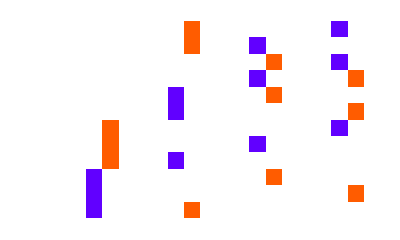
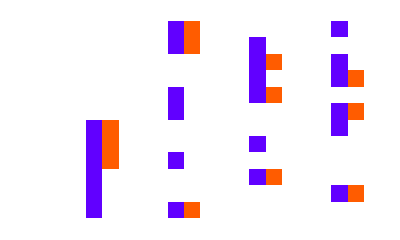
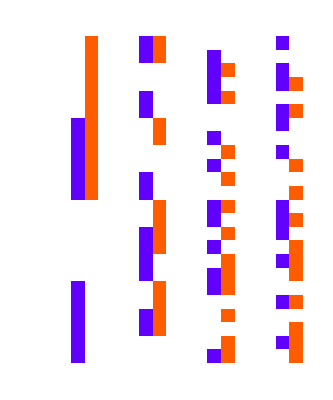

```mathematica
Map[ArrayPlot[#, ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&, Join@@@Permutations[Partition[#[[1, 1]], UpTo[5]]]&/@GatherBy[shuffleevo, Last]]
```

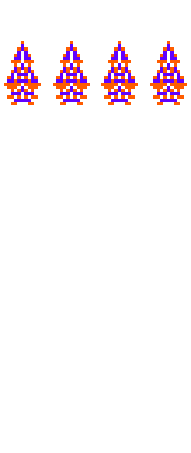
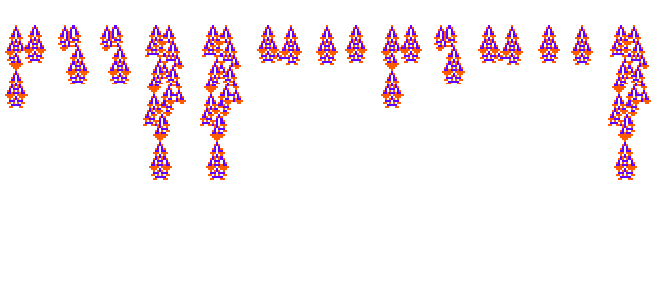
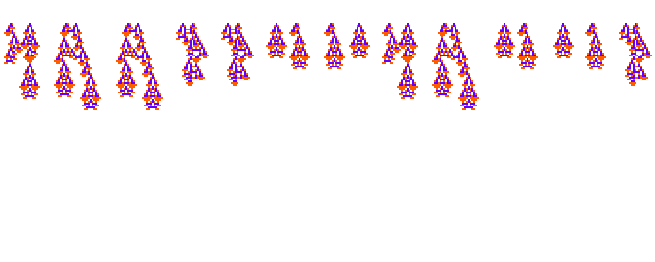
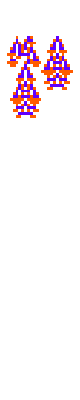
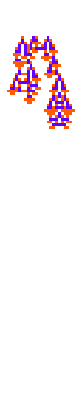
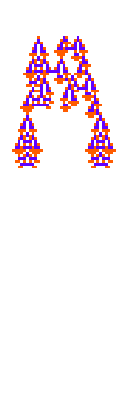
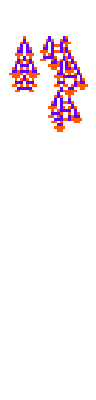
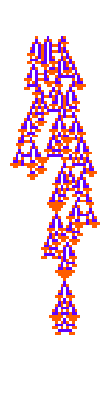
{-Graphics-,-Graphics-,-Graphics-,-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-}

```mathematica
GraphicsRow[ArrayPlot[CellularAutomaton[ru,{#,0},{115, Automatic}], ColorRules->{0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]&/@Join@@@Permutations[Partition[#[[1, 1]], UpTo[5]]]]&/@ GatherBy[shuffleevo, Last]
```

### The bridge to virology

#### Probabilities and the time course of evolution

https://writings.stephenwolfram.com/2024/12/foundations-of-biological-evolution-more-results-more-surprises/#probabilities-and-the-time-course-of-evolution

```mathematica
evolutionGraph=VertexOutComponentGraph[{{"[◼]", "EvolutionaryMultiwayGraph"}}[
{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],
"Reduced"->False,
GraphLayout->"LayeredDigraphEmbedding",
"DistanceFunction"->{{"[◼]", "BinaryMutationDistance"}},
AspectRatio->1],{{0,65815}}];
```

```mathematica
evolutionEdges=GroupBy[Join[
Flatten[Map[Outer[Rule,#,#,1]&,
VertexList[evolutionGraph]],2],
Flatten[MapApply[Outer[Rule,#1,#2,1]&,
EdgeList[evolutionGraph]],2]],First->Last];
```

```mathematica
lftdata=KeyMap[First,{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]];
dataCallouts={{"[◼]", "quickDepict"}}[{2,2},{#,0},lftdata[#]]&/@VertexList[evolutionGraph][[All,1,1]];
```

```mathematica
rules={{"[◼]", "AllSymetricQuiescentRules"}}[2,2];
```

```mathematica
gensIndex=First/@PositionIndex[Union@@evolutionEdges];
```

```mathematica
gensRuleMap=AssociationMap[{{"[◼]", "GenRulesSymmetric"}}[{2,2},#]&,Keys[gensIndex]];
```

```mathematica
gensRuleIndex=Map[{{"[◼]", "SymmetricEncode"}},gensRuleMap,{2}]/2+1;
```

```mathematica
gensRuleIndices=Catenate@Lookup[gensRuleIndex,#]&/@VertexList[evolutionGraph];
```

```mathematica
ruleGensMap=Association@Catenate@KeyValueMap[{g,rs}|->#->Lookup[gensIndex,Key[g]]&/@rs,gensRuleMap];
```

```mathematica
evolutionEdgesIndex=Lookup[gensIndex,#]&/@KeyMap[gensIndex]@evolutionEdges;
```

```mathematica
(*MarkovWeights=SparseArray[Map[rule|->With[{
idx=Lookup[evolutionEdgesIndex,ruleGensMap[rule]],
mutations={{"[◼]", "RuleMutationsList"}}[{rule,2,2},"Symmetric"->True][[All,1]]
},
SparseArray[
With[
{allowedMutations=Select[mutations,MemberQ[idx,ruleGensMap[#]]&]},
Append[{{"[◼]", "SymmetricEncode"}}[rule]/2+1->Length[mutations]-Length[allowedMutations]]@Thread[({{"[◼]", "SymmetricEncode"}}/@allowedMutations)/2+1->1
]
]
,
Length[rules]
]
],rules]];//AbsoluteTiming*)
```

```mathematica
MarkovWeights=Import[CloudObject[["https://www.wolframcloud.com/obj/6a379236-239e-4d1b-b04d-f41ae480d106"](https://www.wolframcloud.com/obj/6a379236-239e-4d1b-b04d-f41ae480d106)]];
```

```mathematica
rulesMarkovMatrix=N[MarkovWeights/Total/@MarkovWeights];
```

```mathematica
data=Transpose[(d|->Total@d[[#]]&/@gensRuleIndices)/@NestList[#.rulesMarkovMatrix&,UnitVector[Length[rules],1],1500]];
```

```mathematica
Block[{data=data[[All,;;1500]],n1=7,n2=4,x=300,ordering1,ordering2},
ordering1=Reverse@Ordering@data[[All,-1]];
ordering2=Reverse@Ordering@data[[ordering1,x]];
StackedListPlot[data[[ordering1]],Epilog->Reverse@Join[
MapThread[Inset[#1,{Length[data[[1]]]0.95,#2},Automatic,Scaled[.07]]&,{dataCallouts[[ordering1[[;;n1]]]],Mean/@Partition[Prepend[0]@Accumulate[data[[ordering1]][[;;n1,-1]]],2,1]}]
,
MapThread[Inset[#1,{x,#2},Automatic,Scaled[.07]]&,{dataCallouts[[ordering1[[ordering2]][[;;n2]]]],Mean/@Partition[Prepend[0]@Accumulate[data[[ordering1,x]]],2,1][[ordering2[[;;n2]]]]}]
]
]
]
```

-Graphics-

https://nextstrain.org/sars-cov-2/forecasts

#### Evolutionary multiway graph

From: https://writings.stephenwolfram.com/2024/12/foundations-of-biological-evolution-more-results-more-surprises/#multiway-graphs-for-larger-rule-spaces

```mathematica
Module[{gk2r2,embedding},
gk2r2=WeaklyConnectedGraphComponents[
Import[CloudObject[["https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c"](https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c)]],
AspectRatio->2/3][[1]];
SeedRandom[12345];
embedding=Map[#+RandomReal[20,2]&,
GraphEmbedding[gk2r2]];
Graph[gk2r2,EdgeStyle->Directive[Hue[0.6,0.4,0.5,.6],Opacity[.15]],
VertexStyle->GrayLevel[.3],VertexCoordinates->embedding]
]
```

```mathematica
gk2r2=WeaklyConnectedGraphComponents[
Import[CloudObject[["https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c"](https://www.wolframcloud.com/obj/87be2e58-f0cd-4472-8dba-fc4c9a00af0c)]],
AspectRatio->2/3][[1]];
```

```mathematica
gk2r2
```

-Graphics-

```mathematica
{VertexConnectivity[gk2r2], EdgeConnectivity[gk2r2], GraphDensity[gk2r2], GraphLinkEfficiency[gk2r2], GraphReciprocity[gk2r2]}
```

{0,0,277/414348,-∞,0}

TODO: Compare to multiway from  https://nextstrain.org/ncov/gisaid/global/6m

### Distribution in Morphospace (SW)

```mathematica
mgraph={{"[◼]", "addVertexFigures"}}[VertexReplace[NearestNeighborGraph[Keys[{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]],{All,3/2},DistanceFunction->{{"[◼]", "BinaryMutationDistance"}}],x_:>{x}],{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],{2,2},EdgeStyle->Gray,VertexSize->1/2];
```

```mathematica
allpix=ArrayPlot[ArrayPad[#,1]&/@CellularAutomaton[{#[[1,1]],2,2},{{1},0},{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"][#[[1]]]+1],ImageSize->Tiny]&/@VertexList[mgraph];
```

```mathematica
FeatureSpacePlot[allpix,RandomSeeding->456,Method->"UMAP",AspectRatio->1/GoldenRatio,Frame->True,FrameStyle->Gray,FrameTicks->None]
```

### Host parasite perturbation battle

#### Less aggressive

```mathematica
therapyevo = 
Module[{ i = 5, ltgoal ,  pca,llt, ca, initpert = <|{23,111}->2|>, initca, initlt, initaps,
plt, ru = {299459058088077823758143088095350287424,4,1}},
SeedRandom[333557 + i];
initca = {{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {200, {-110, 110}}, initpert];
initlt = Replace[{{"[◼]", "TestCALifeTime"}}[initca], -Infinity:> 401];
initaps = Select[{{"[◼]", "allperts"}}[First[initca], ru[[2]]], Keys[#][[1, 1]]>= Keys[initpert][[-1, 1]]&];
ltgoal = normlt =  {{"[◼]", "TestCALifeTime"}}[ CellularAutomaton[ru, {{1}, 0}, {200, {-110, 110}}]];
j = 0;
Reap[Sow[{initpert, initlt, initlt}];
NestWhile[
Function[{fitness, perts, aps},
pca = {{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {400, {-110, 110}}, Join[perts, RandomChoice[aps]]];
llt={{"[◼]", "TestCALifeTime"}}[First[pca]];plt = Replace[llt, -Infinity:> 401];
ltgoal = If[EvenQ[j], normlt, initlt];
Sow[{Last[pca],llt,If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal],plt,fitness]}];
If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal], j = j +1;{plt, Join[perts, Last[pca]],Select[{{"[◼]", "allperts"}}[First[pca], ru[[2]]], Keys[#][[1, 1]]>= Keys[Last[pca]][[-1, 1]]&]}, {fitness, perts, aps}]
]@@#&, {initlt,initpert, initaps},Last[#]=!={}&,1,14]][[2, 1]]];
```

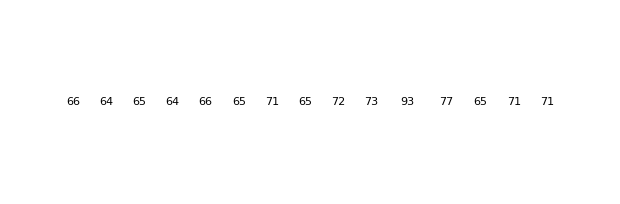

```mathematica
GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}}, #[[1]]],FrameStyle->If[#[[2]]==#[[3]],Directive[Black,Thick],Automatic],ImageSize->{Automatic,180}],Text[Style[#[[2]],Small]]]&/@therapyevo]
```

#### More aggressive

Odd number trying to stay at the sick state, even number trying to get back to the healthy state

```mathematica
txiseq[i_,cut_,max_]:=Module[{plt,ilt,iaps,ru={299459058088077823758143088095350287424,4,1},ip=<|{23,111}->2|>,ica},ica = {{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {200, {-110, 110}}, ip];ilt = Replace[{{"[◼]", "TestCALifeTime"}}[ica], -Infinity:> 401];
iaps = Select[{{"[◼]", "allperts"}}[First[ica], ru[[2]]], Keys[#][[1,1]]-Keys[ip][[-1,1]]==cut&];
ltgoal = normlt =  {{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru, {{1}, 0}, {200, {-110, 110}}]];With[{ttt=
Module[{ ltgoal ={{"[◼]", "TestCALifeTime"}}[CellularAutomaton[ru, {{1}, 0}, 400]], pca,llt},
SeedRandom[333557 + i];
j = 0;
Reap[Sow[{ip}];NestWhileList[
Function[{fitness, perts, aps},
pca = {{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {400, {-110, 110}}, Join[perts, RandomChoice[aps]]];
llt={{"[◼]", "TestCALifeTime"}}[First[pca]];plt = Replace[llt, -Infinity:> 401];
ltgoal = If[EvenQ[j], normlt, ilt];
Sow[{Last[pca],llt,If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal],plt,fitness]}];
If[Abs[plt - ltgoal] <= Abs[fitness-ltgoal], j = j + 1;{plt, Join[perts, Last[pca]],Select[{{"[◼]", "allperts"}}[First[pca], ru[[2]]],Keys[#][[1,1]]-Keys[Last[pca]][[-1,1]]==cut&]}, {fitness, perts, aps}]
]@@#&, {ilt,ip, iaps},Last[#]=!={}&,1,max]]]},With[{u=Cases[ttt[[2,1]],{_,x_,x_}]},First/@Split[Take[u,If[!IntegerQ[#],Length[u],First@#]&[FirstPosition[Last/@u,101]]]]]]]
```

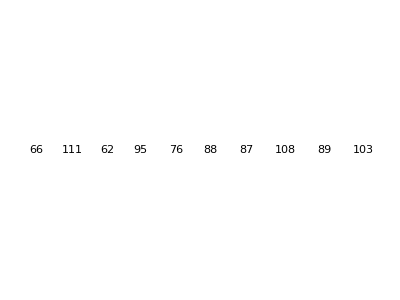

```mathematica
GraphicsGrid[Partition[Labeled[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1}, {{1}, 0}, {105, {-110, 110}}, #[[1]]],ImageSize->{Automatic,180}],Text[Style[#[[2]],Small]]]&/@Prepend[txiseq[10,1,20],{<|{23,111}->2|>,66,66}],10],Spacings->12]
```

### Perturbed Gene Evolution

Should run at scale with AWS to see what these guys look like, I bet they’ll look interesting

```mathematica
SeedRandom[4447];
als = Reap[
evo=NestList[Module[{}, 
ru={{"[◼]", "RandomRuleMutation"}}[First[#]];
ca = CellularAutomaton[ru, {{1}, 0}, 100];
lt = {{"[◼]", "TestCALifeTime"}}[ca];
rus =Table[{{"[◼]", "RandomRuleMutation"}}[ru], Floor[If[# == -Infinity, 0, #]&[Min[Last[#]]] / 10]];
cas= CellularAutomaton[#, {{1}, 0}, 100]&/@ rus;
lts=Prepend[{{"[◼]", "TestCALifeTime"}}/@ cas, lt];
Sow[lts];
If[Min[lts]>=Min[Last[#]],{ru,lts},#]
]&,{{0,4,1},{0, 0}},500]][[2, 1]];
```

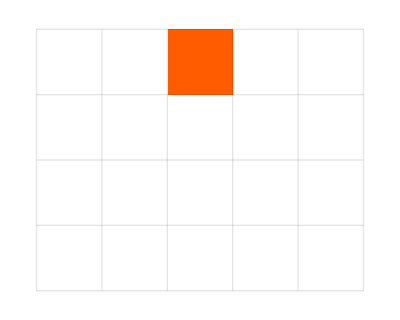
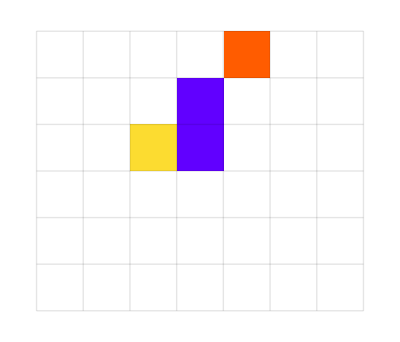
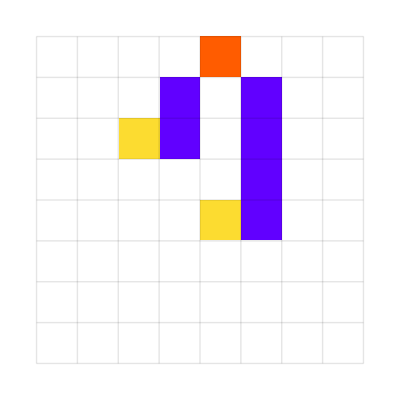
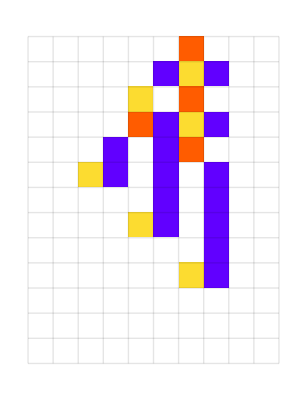
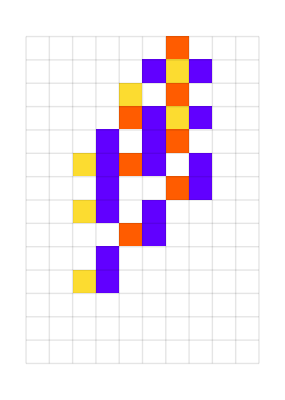
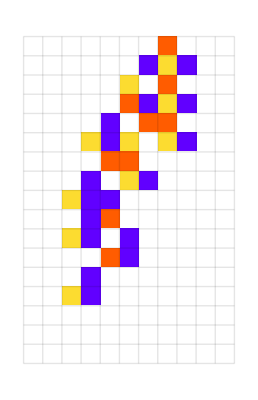
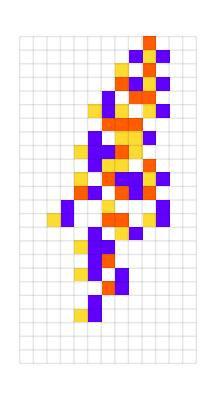
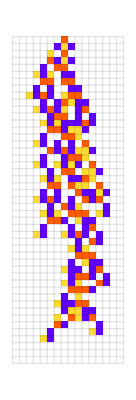
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
e2=Rest[First/@SplitBy[evo,Last]];
Map[CompoundExpression[
data=CellularAutomaton[
First[#],{{1},0},#[[-1, 1]]+2],
data=ArrayPad[#,2]&/@data,
ArrayPlot[data,ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],
ImageSize->{Automatic,26Sqrt[Length[data]+1]},
Mesh->True,MeshStyle->Opacity[.1]
]
]&,
e2]
```

### Changing fitness function

https://writings.stephenwolfram.com/2024/12/foundations-of-biological-evolution-more-results-more-surprises/#the-macroscopic-flow-of-evolution

```mathematica
gens=Keys[{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"]];
```

```mathematica
gensCallouts={{"[◼]", "quickDepict"}}[{2,2},#,{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"][#]]&/@gens;
```

```mathematica
{gensRuleMap,ruleGensMap}={{"[◼]", "MarkovRuleMap"}}[First/@PositionIndex[gens]];
```

```mathematica
size=Length[ruleGensMap];
```

```mathematica
ruleIndex=AssociationThread[Keys[ruleGensMap],Range[size]];
```

```mathematica
gensRuleIndices=Lookup[gensRuleMap,Key@#]&/@gens;
```

(Long computation time + 8 GB)

```mathematica
arMarkovWeights=Parallelize@AssociationMap[{{"[◼]", "FitnessMarkovWeights"}}[{{"[◼]", "arFitness"}}[#]]&,Union[Range[120]/100,Range[600,900]/1000]];
```

$Aborted

```mathematica
arMarkovMatrices=N[#/Total/@#]&/@arMarkovWeights;
```

```mathematica
arfollowing[schedule_]:=With[{arScheduleData=Catenate@FoldList[With[{matrix=arMarkovMatrices[First[#2]]},Rest[NestList[#.matrix&,#1[[-1]],Length[#2]]]]&,{UnitVector[Length[arMarkovMatrices[[1]]],1]},Split[#]]&@schedule},Total/@arScheduleData[[All,Lookup[ruleIndex,#]]]&/@gensRuleIndices]
```

```mathematica
With[{sc=Table[First@Nearest[Union[Range[120]/100,Range[600,900]/1000],1.2t /2500],{t,1,2500}]},
ListLinePlot[MapThread[Which[Max[#1]>.2,With[{x=PositionLargest[#1,1][[1,1]]},Callout[#1,#2,x]],Max[#1]>.1,Callout[#1,#2],True,#1]&,{#2,gensCallouts}],PlotRange->Full,Frame->True,Epilog->Inset[ListStepPlot[#1,PlotStyle->Red,Frame->True],Scaled[{1,.95}],{Right,Top},Scaled[.35{1,1}]]]&[sc,arfollowing[sc]]]
```

#### Back and forth between 10 and 30

#### Periodic fitness function (WN)

TODO: Sine function

```mathematica
i = 0;
target =10;
evo=NestList[CompoundExpression[
i = i + 1,
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
life={{"[◼]", "TestLifetime"}}[ru],
target = If[Mod[i, 200] == 0,If[target == 10, 30, 10], target],
If[Abs[life  - target]<=Abs[Last[#] -target],{ru,life},#]
]&,{{0,4,1},0},2000];
```

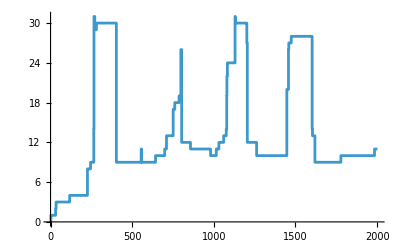

```mathematica
ListStepPlot[evo[[All, -1]]]
```

### More Relevant People

Luis Zaman, Lanny Kirsch, Mohammed AlQuraishi

## A Generalized Computational Framework for Distinguishing Engineered and Adapted Systems

### In GOL post

#### Adapted: https://writings.stephenwolfram.com/2025/03/what-can-we-learn-about-engineering-and-innovation-from-half-a-century-of-the-game-of-life-cellular-automaton/#the-comparison-with-adaptive-evolution

```mathematica
TestCALifetime2D[ca_List]:= If[#==0,-Infinity,Length[ca]-#]&[LengthWhile[Reverse[ca],Total[#,2]==0&]]
```

```mathematica
aseq=(SeedRandom[34578+126];With[{max=400},NestList[Module[{u=MapAt[1-#&,#[[1]],RandomInteger[{1,16},2]],lt},lt=TestCALifetime2D[CellularAutomaton["GameOfLife",{u,0},max]];If[lt>0&&lt>=#[[2]],{u,lt},#]]&,{RandomInteger[1,{16,16}],0},2000]]);
```

$Aborted

```mathematica
GraphicsRow[(Labeled[{{"[◼]", "CellularAutomatonPlot3D"}}["GameOfLife",{#[[1,1]],0},1+#[[1,2]],ImageSize->{Automatic,20Sqrt[#[[1,2]]+4]}],If[#[[1,2]]>0,Style[Text[#[[1,2]]],GrayLevel[0.25]],""]]&/@SplitBy[#,Last])&[aseq]]
```

#### Engineered vs. searched: https://writings.stephenwolfram.com/2025/03/what-can-we-learn-about-engineering-and-innovation-from-half-a-century-of-the-game-of-life-cellular-automaton/#invented-or-discovered-made-for-a-purpose-at-all

ResourceObjectupdav4f6346d9-9fdb-47e5-9d40-b1f5d682887b27127797808624712300830Local

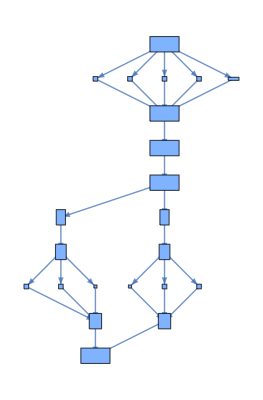
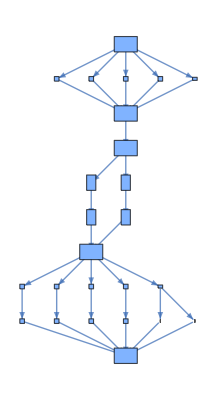
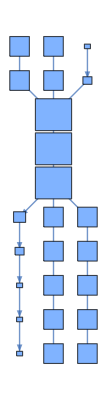
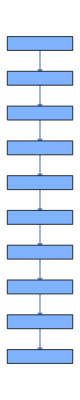
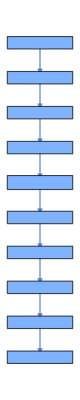
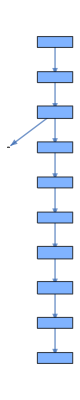
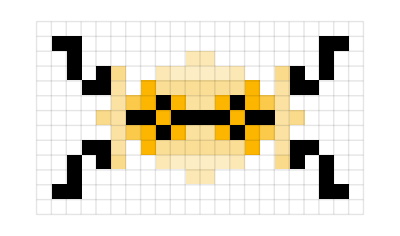
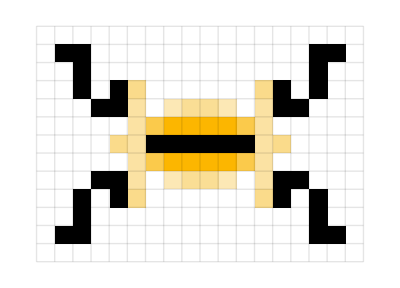
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
1972 | 1972 | 1984 | 1997 | 1998 | 2014-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2018 | 2020 | 2021 | 2022 | 2023

```mathematica
vertfunc = Function[{pos,val,blah},Rectangle[pos-#/45,pos+#/45]&@(Subtract@@(Reverse@MinMax[#])&/@Transpose[Ramp[val[[-1]]]])];
Style[Row[With[{elems=With[{data=Select[ResourceData["LifeWiki Dataset 2025"],#Class === "Oscillator" && #Period ==9&]},MapIndexed[{Graph[{{"[◼]", "BoundingBoxLayeredGraph"}}[#, Automatic, VertexShapeFunction->vertfunc],ImageSize->{Automatic,130}],{{"[◼]", "CellularAutomatonHistoryPlot"}}["GameOfLife",{#MatrixData,0},9,ImageSize->13Sqrt[Reverse@Dimensions[#1["MatrixData"]]]],Text[Style[#Year,Small,GrayLevel[0.25]]]}&,Values[SortBy[data//Quiet,#Year&]]]]},Grid[Transpose[#],Dividers->{All,False},FrameStyle->GrayLevel[.7],Alignment->Center]&/@Partition[elems, UpTo[6]]]],LineSpacing->{1,40}]
```

### In Biol-Evol

https://writings.stephenwolfram.com/2024/12/foundations-of-biological-evolution-more-results-more-surprises/#random-or-selected-can-one-tell

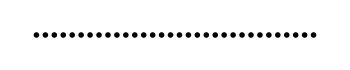
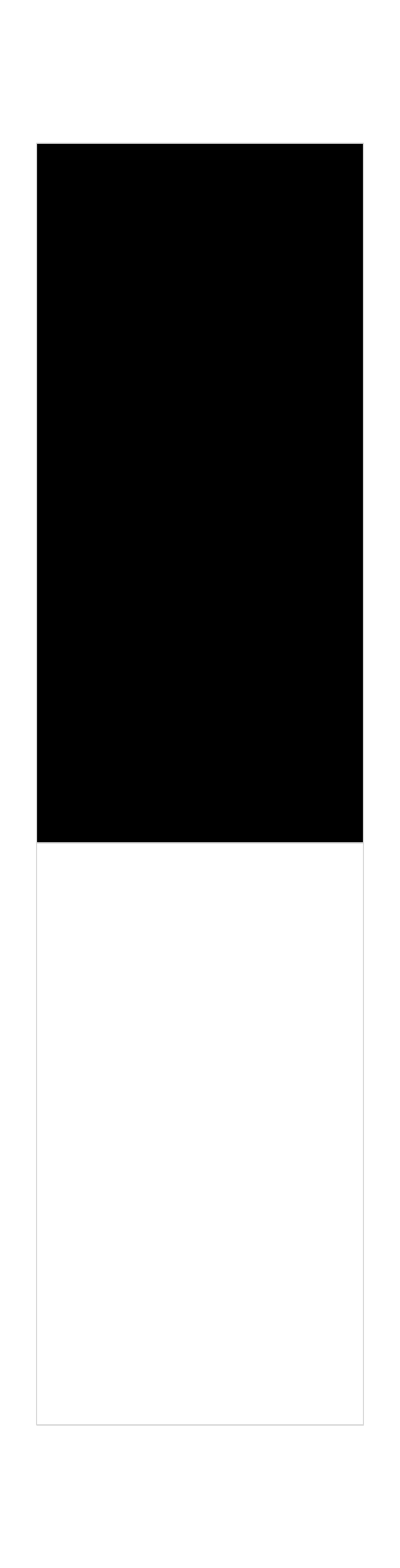
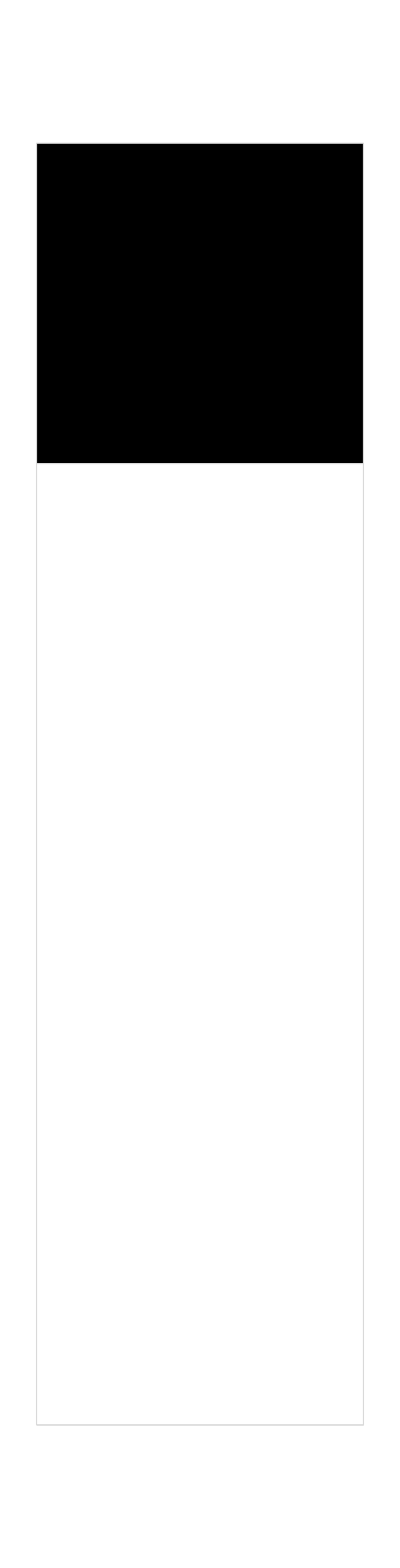
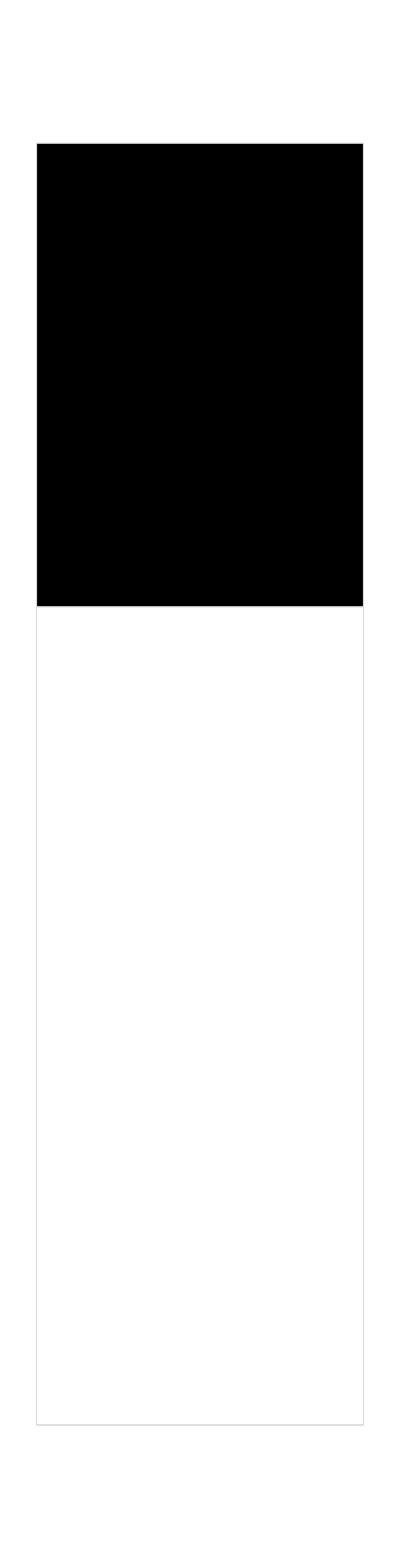
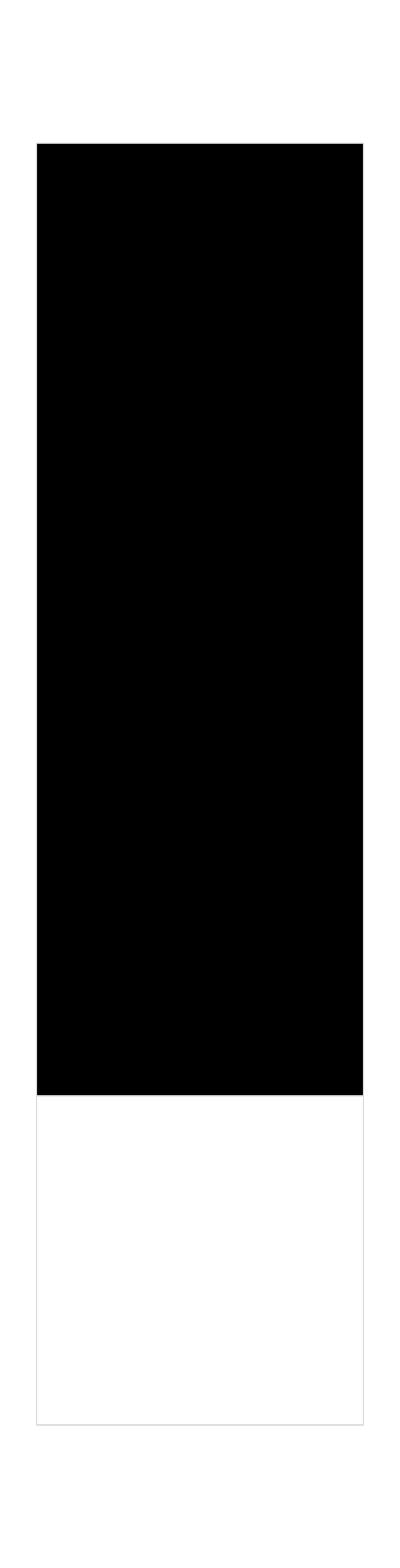
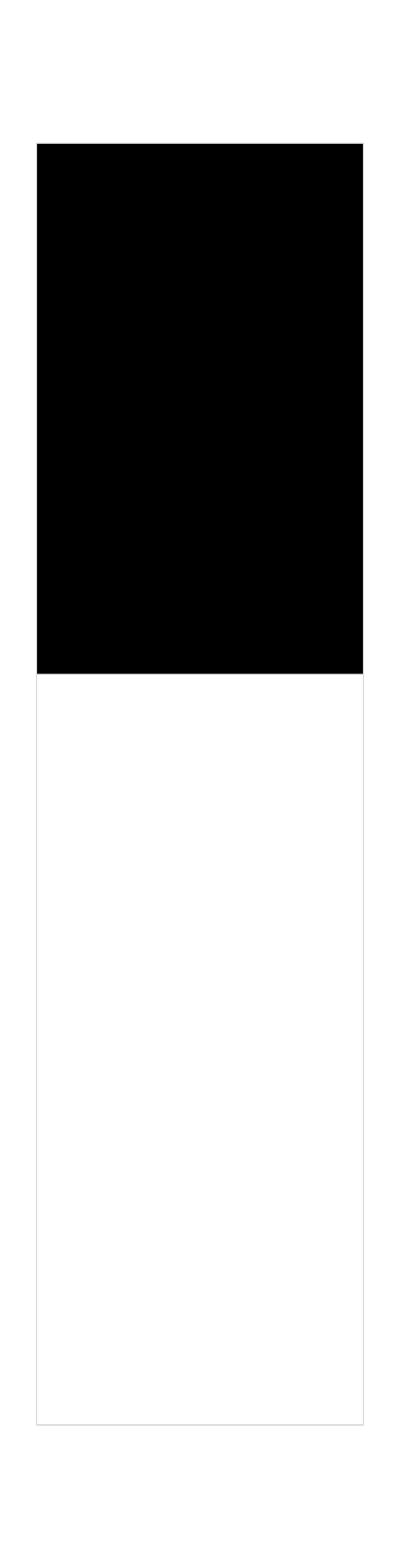
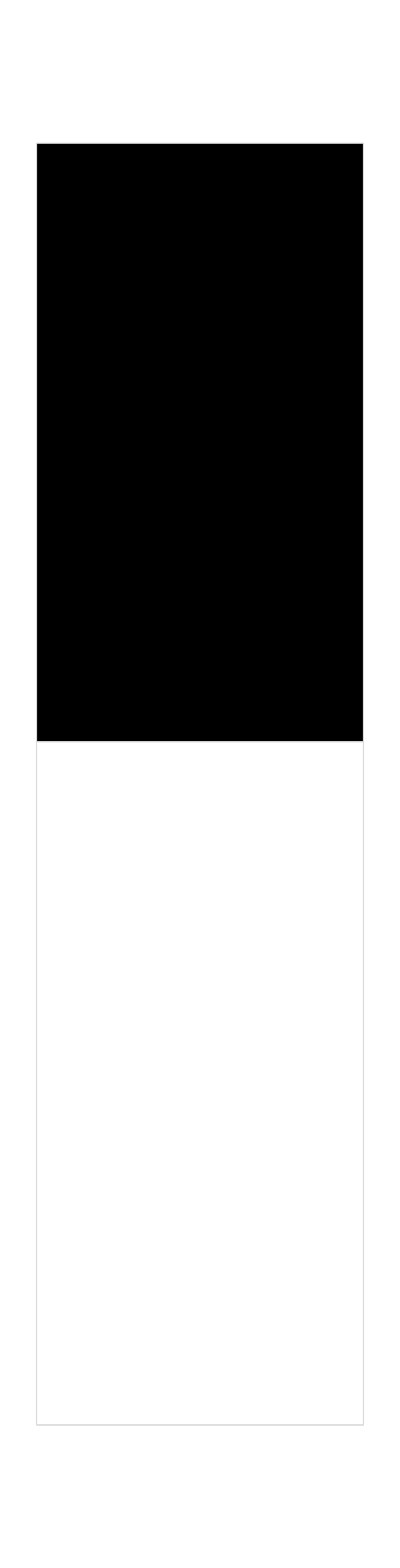
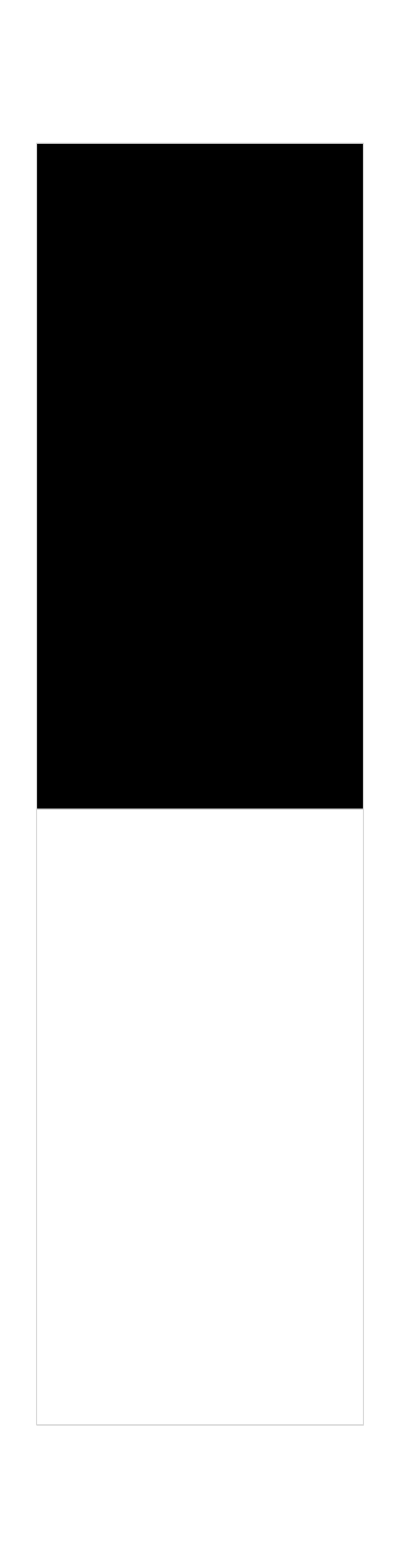
-Graphics-all genotypes
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-"viable" genotypes
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-lifetime > 10
-Graphics-lifetime > 25

```mathematica
Column[MapThread[Labeled[#1,Style[Text[#2],Gray],Right]&,{Prepend[GraphicsRow[Map[Graphics[MapIndexed[{EdgeForm[LightGray],Association[1->White,2->Black][#2[[1]]],Rectangle[{0,#1[[1]]},{1,#1[[2]]}]}&,{{0,1/2},{1/2,1}}],AspectRatio->4,Axes->False]&,Range[32]],ImageSize->350]][Table[GraphicsRow[Map[Graphics[MapIndexed[{EdgeForm[LightGray],Association[1->Gray,2->White,3->Black][#2[[1]]],Rectangle[{0,#1[[1]]},{1,#1[[2]]}]}&,Partition[Prepend[Accumulate[{0,#[[1]]/2+#[[2]],#1[[1]]/2+#[[3]]}&@Lookup[Counts[#],{0,1,2},0]],0],2,1]],AspectRatio->4,Axes->False]&,Transpose[Map[If[#[[1]]==0,0,1+#[[2]]]&/@Transpose[{IntegerDigits[#[[2]],2,32],IntegerDigits[#[[1]],2,32]}]&,Keys[Select[{{"[◼]", "$LifetimeData"}}[2,2,"Symmetric"],#>u&]]]]],ImageSize->350],{u,{0,10,25}}]],{"all genotypes","\"viable\" genotypes","lifetime > 10","lifetime > 25"}}]]
```

#### Using Classify to predict whether a rule is random (no immunity), adapted (width immunity), or adapted (height immunity)

Results: It actually works with 80% accuracy, I have no idea how it works

```mathematica
SeedRandom[444555];
rand = Append[#,0]&/@RandomChoice[{0,1,2},{100,3^(2*1+1)-1}];
widthdigs = Module[{digits,n,k,r},{n,k,r}=interpretrule[#];
digits=IntegerDigits[n,k,k^(2r+1)]]&/@widthruns[[All, -1, 1]];
heightdigs = Module[{digits,n,k,r},{n,k,r}=interpretrule[#];
digits=IntegerDigits[n,k,k^(2r+1)]]&/@runs[[All, -1, 1]];
all = Join[Thread[rand->"Random"], Thread[widthdigs->"Width"], Thread[heightdigs->"Height"]];
```

```mathematica
SeedRandom[5555];
trainidxs = RandomSample[Range[Length[all]], 250];
testidxs = RandomSample[Delete[Range[Length[all]], List/@ trainidxs], All];
```

```mathematica
cf = Classify[all[[trainidxs]]]
```

ClassifierFunction[…]

```mathematica
cs  = cf/@ all[[testidxs, 1]];
```

```mathematica
With[{bools = MapThread[If[#1 === #2, True, False]&, {cs, all[[testidxs, 2]]}]},
N[Count[bools, True]/ Length[bools]]]
```

0.8

### Machine learning:

https://writings.stephenwolfram.com/2024/08/whats-really-going-on-in-machine-learning-some-minimal-models/#machine-learning-in-discrete-rule-arrays

#### Adapted

```mathematica
Options[RuleArray]={"Radius"->1/2,"Orientation"->"Both","Neighborhood"->"Alternating","Function"->"FinalState"};
```

```mathematica
RuleArray[opts:OptionsPattern[RuleArray]]:=RuleArray[OptionValue["Radius"],OptionValue["Orientation"],OptionValue["Neighborhood"],OptionValue["Function"]]

RuleArray[radius_,orientation_,neighborhood_,function_]:=Function[{
Typed[initialState,"PackedArray"::["MachineInteger",1]],
Typed[ruleArray,"PackedArray"::["MachineInteger",If[orientation=="Both",2,1]]],
Typed[numSteps,"MachineInteger"]
},
Module[{i, state, states,raHeight,raWidth,raElement},
state=initialState;

If[function=="Lifetime",If[Total[state]==0,Return[0]]];

If[function=="States",states={state}];

raHeight=If[orientation=="Vertical",numSteps,Length[ruleArray]];
raWidth=If[orientation=="Vertical",Length[ruleArray],Length[initialState]];

i=1;
While[i<=raHeight,
If[orientation=="Horizontal",
raElement=ruleArray[[i]];
];

state=Table[
Module[{left, center,right,input},
If[orientation=="Both",
raElement=ruleArray[[i,j]];
,If[orientation=="Vertical",
raElement=ruleArray[[j]];
];
];

left=If[j==1,state[[-1]],state[[j-1]]];
center=state[[j]];
right=If[j==raWidth,state[[1]],state[[j+1]]];

If[radius==1,
input=BitOr[BitShiftLeft[left,2],BitShiftLeft[center,1],right];
,If[radius==1/2,
If[neighborhood=="LeftCenter",
input=BitOr[BitShiftLeft[left,1],center];
,If[neighborhood=="RightCenter",
input=BitOr[BitShiftLeft[center,1],right];
,If[neighborhood=="Alternating",
input=If[Mod[i,2]==1,BitOr[BitShiftLeft[center,1],right],BitOr[BitShiftLeft[left,1],center]];
]
]
]
]
];

BitShiftRight[BitAnd[raElement,BitShiftLeft[1,input]],input]
],{j,raWidth}];

If[function=="States",
AppendTo[states,state];
,If[function=="Lifetime",
If[Total[state]==0,
Return[i];
];
]
];

++i;
];

If[function=="FinalState",
state
,If[function=="States",
states
,If[function=="Lifetime",
i
]
]
]
]
];
```

```mathematica
MetaRuleArray[opts:OptionsPattern[RuleArray]]:=RuleArray["Radius"->radius,"Orientation"->orientation,"Neighborhood"->neighborhood,"Function"->function]/.{
radius->OptionValue["Radius"],
orientation->OptionValue["Orientation"],
neighborhood->OptionValue["Neighborhood"],
function->OptionValue["Function"]
}//.{
If[cond_,true_]/;cond==True:>true,
If[cond_,true_]/;cond==False:>Null,
If[cond_,true_,else_]/;cond==True:>true,
If[cond_,true_,else_]/;cond==False:>else
}
```

```mathematica
RuleArrayFinalState[opts:OptionsPattern[RuleArray]][initialState_,ruleArray_,numSteps_Integer]:=MetaRuleArray[opts,"Function"->"FinalState"][initialState,ruleArray,numSteps];
RuleArrayStates[opts:OptionsPattern[RuleArray]][initialState_,ruleArray_,numSteps_Integer]:=MetaRuleArray[opts,"Function"->"States"][initialState,ruleArray,numSteps];
RuleArrayLifetime[opts:OptionsPattern[RuleArray]][initialState_,ruleArray_,numSteps_Integer]:=MetaRuleArray[opts,"Function"->"Lifetime"][initialState,ruleArray,numSteps];
```

```mathematica
NormalizeRuleArray[raHeight_Integer,raWidth_Integer,ruleArray_List,opts:OptionsPattern[RuleArray]]/;And[OptionValue[RuleArray,{opts},"Orientation"]=="Both",Dimensions[ruleArray]=={raHeight,raWidth}]:=ruleArray
NormalizeRuleArray[raHeight_Integer,raWidth_Integer,ruleArray_List,opts:OptionsPattern[RuleArray]]/;And[OptionValue[RuleArray,{opts},"Orientation"]=="Horizontal",Dimensions[ruleArray]=={raHeight}]:=Transpose[Table[ruleArray,raWidth]]
NormalizeRuleArray[raHeight_Integer,raWidth_Integer,ruleArray_List,opts:OptionsPattern[RuleArray]]/;And[OptionValue[RuleArray,{opts},"Orientation"]=="Vertical",Dimensions[ruleArray]=={raWidth}]:=Table[ruleArray,raHeight]
```

```mathematica
LifetimeLossValue[life_Integer,target_Integer,tmax_Integer]:=If[life==tmax,Infinity,Abs[(life-target)]]
LifetimeLoss[targetHeight_Integer][raHeight_Integer,raWidth_Integer,opts:OptionsPattern[RuleArray]][ruleArray_List]:=With[{lifetimeFn=RuleArrayLifetime[opts]},LifetimeLossValue[lifetimeFn[CenterArray[1,raWidth],ruleArray,raHeight],targetHeight,raHeight+1]
]
```

```mathematica
MutateRuleArray[ruleArray_List,nRules_Integer,opts:OptionsPattern[RuleArray]]/;(OptionValue[RuleArray,{opts},"Orientation"]!="Both"):=Module[{raLength,i,j,val,newVal},
{raLength}=Dimensions[ruleArray];
i = RandomInteger[{1,raLength}];
val=ruleArray[[i]];
newVal=Mod[val-1+RandomInteger[{1,nRules-1}],nRules]+1;
ReplacePart[ruleArray,{i}->newVal]
]

MutateRuleArray[ruleArray_List,nRules_Integer,opts:OptionsPattern[RuleArray]]/;(OptionValue[RuleArray,{opts},"Orientation"]=="Both"):=Module[{raHeight,raWidth,i,j,val,newVal},
{raHeight,raWidth}=Dimensions[ruleArray];
i = RandomInteger[{1,raHeight}];
j = RandomInteger[{1,raWidth}];
val=ruleArray[[i,j]];
newVal=Mod[val-1+RandomInteger[{1,nRules-1}],nRules]+1;
ReplacePart[ruleArray,{i,j}->newVal]
]
```

```mathematica
IndicesToRules[indices_List,rules_List,opts:OptionsPattern[RuleArray]]/;(OptionValue[RuleArray,{opts},"Orientation"]!="Both"):=Map[rules[[#]]&,indices]
IndicesToRules[indices_List,rules_List,opts:OptionsPattern[RuleArray]]/;(OptionValue[RuleArray,{opts},"Orientation"]=="Both"):=Map[rules[[#]]&,indices,{2}]
```

```mathematica
AdaptRuleArray[ruleArray_List,rules_List,maxIters_Integer,lossFn_,opts:OptionsPattern[RuleArray]]:=With[{actrules=MapThread[Rule,{Range[Length[rules]],rules}]},NestWhileList[Module[{m=MutateRuleArray[#[[1]],Length[rules],opts],lo},lo=lossFn[IndicesToRules[m,rules,opts]];If[lo<=#[[2]],{m,lo},#]]&,{ruleArray,lossFn[IndicesToRules[ruleArray,rules,opts]]},Last[#]>0&,1,maxIters]]
```

```mathematica
(*evols=ParallelTable[
SeedRandom[234234+i];
With[{raHeight=64,raWidth=31,rules={4,146},opts=Sequence["Radius"->1,"Orientation"->"Both"],loss=LifetimeLoss[50]},
With[{lossFn=loss[raHeight,raWidth,opts]},
First@Last@AdaptRuleArray[ConstantArray[1,{raHeight,raWidth}],rules,10000,lossFn,opts]
]
],{i,1,100}];*)
```

```mathematica
evols=CloudImport[CloudObject[["https://www.wolframcloud.com/obj/6afaa277-fdad-495c-aa99-135563f088b7"](https://www.wolframcloud.com/obj/6afaa277-fdad-495c-aa99-135563f088b7)]];
```

```mathematica
GraphicsGrid[Partition[Table[With[{raHeight=64,raWidth=31,lifetimeTarget=50,rules={4,146},opts=Sequence["Radius"->1,"Orientation"->"Both","Mesh"->False,"RuleColors"->{Hue[0.5, 0.4, 0.9],Hue[0.86, 0.4, 0.9]},"Lightness"->0],ruleArray=evols[[i]]},
{{"[◼]", "ICAEvolutionPlot"}}[raHeight,raWidth,ruleArray,rules,CenterArray[1,{raWidth}],opts,Epilog->{
Opacity[0.25],
Line[{{0,raHeight},{raWidth,raHeight}}],
Opacity[0.25],
Line[{{0,raHeight-lifetimeTarget+1},{raWidth,raHeight-lifetimeTarget+1}}]
}]
],{i,{1,2,3,4,5,6,7,90,97,89,20,13}}],6]]
```

-Graphics-

#### Engineered

```mathematica
GraphicsGrid[Partition[With[{raHeight=11,raWidth=15,rules={4,146},opts=Sequence["Radius"->1,"Orientation"->"Both","Mesh"->True,"RuleColors"->{Hue[0.5, 0.4, 0.9],Hue[0.86, 0.4, 0.9]},"Lightness"->0],ruleArray=#},
{{"[◼]", "ICAEvolutionPlot"}}[raHeight,raWidth,ruleArray,rules,CenterArray[1,{raWidth}],opts,Epilog->{
Opacity[0.25],
Line[{{0,raHeight},{raWidth,raHeight}}]
}]
]&/@Table[ReplacePart[Table[1,11,15],{2i,7}->2],{i,5}],4]]
```

-Graphics-

### Adapted vs. engineered vs. searched doubling CA (WN)

#### Adapted

```mathematica
(*evo = Module[
{deep=500,cut=100(*,ru, cas, outputs, fit*)},
SeedRandom[426785];
NestList[CompoundExpression[
ru={{"[◼]", "RandomRuleMutation"}}[First[#]],
cas = Table[CellularAutomaton[ru,Join[Table[1,j],{2}], cut], {j, 5}],
outputs = Length[{{"[◼]", "nonzeroRange"}}[#[[-1]]]]&/@ cas,
fit = Total[Abs[{4, 6, 8, 10, 12} - outputs]],
If[fit<=Last[#],{ru,fit},#]
]&,{{0, 4, 1},40},deep]
];*)
```

```mathematica
evo = ;
```

```mathematica
Table[ArrayPlot[ArrayPad[#, 5]&/@CellularAutomaton[evo[[-1, 1]],Join[Table[1,j],{2}], 50],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]], {j, 5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Engineered

```mathematica
Module[{rule = {240824173972169928683754419908854649632358071021339860885215426593721945630946574283651280613598854833431614349946624957254166853188064946498713886501186055046270857664, 6, 1}, ca,capert,  pert = <|{3,7}->4|>, colrules = Join[{0->White, 1->Darker[Blue]},Table[ i->Blend[{White, LightBlue, Blue}, i/5], {i, 2, 5}]]},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{80,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, ImageSize-> {Automatic, 250}, "InitialIndex"->0]]@@@#]&/@caperts[[{1}]]
]
```

{-Graphics-}

#### Search

```mathematica
SeedRandom[111000+8];Module[{rule = {837428508144, 3, 1}, ca,capert,  pert = <|{30,9}->2|>, colrules = {0->White, 1->Darker[Blue], 2->RGBColor[0.696, 0.752, 1]}, caperts},
caperts = Table[[rule, {Join[Table[1,j],{2}],0},{60,{-5, 15}}, #], {j, 1, 5}]&/@ {<||>, pert};
GraphicsRow[Function[{ca, pert},{{"[◼]", "PerturbedArrayPlot"}}[ca, If[pert == <||>, {}, First[Keys[pert]]],ColorRules->colrules, Mesh->True, MeshStyle->Opacity[.1],"ArrowStyle"->Directive[Arrowheads[Large],GrayLevel[.9], Haloing[Red]],"ArrowDirection"->Left, ImageSize-> {Automatic, 250}]]@@@#]&/@caperts[[{1}]]
]
```

{-Graphics-}